# Video Traking

User interface for video traking by Karolis Misiunas. 
Warning: The routine works slightly differently on Mac and Windowns since M9+ because FFmpeg library is not compatable.

ToDo:
 - [ ] Add multiple ROI processing in UI
 - [ ] Reporting: Running analysis reporting as Monitor[]
 - [ ] FFmpeg: optimise for speed (it is not a bottle neck, but would be nice to have additional ~15%
 - [ ] Processing: run on multiple cores - will speed it up a lot!
 - [ ] Localised intensity correction for treshhold
 - [ ] FFImport frame count is not working properly or relies on Import[]
 - find out what happens when there is poor particle and a good one in intire analysis - might be we include them as singles?!

```mathematica
Quit[];
```

```mathematica
<<VideoAnalysis`
$HistoryLength = 2; (*prevent memory overload*)
SetOptions[FFmpeg, 
  "Colors"->1 (*number of color channels*),
  "ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
];
SetOptions[VideoIO,
  "FrameIdFromFrame"-> True,
  "Import" -> FFImport
];
```

## Under the hood functions

```mathematica
FindIntervals[raw_]:= Module[{list},
  list = Sort[ DeleteDuplicates[raw]];
  If[ Length[list] == 0, Return[{}]]; 
  Append[ 
  Reap[FoldList[
    If[#2-Last[#1]==1,
      Append[#1,#2],
      If[Length[#1]==1, Sow[First[#1]], Sow[Interval[{First[#1],Last[#1]}]]];
      {#2}] & ,
    {First[raw]},
    Rest[list]]][[-1,1]],Last[list] 
  ] 
];

processVideo[file_] := Module[{loadTime, analysisTime,oldROI,outputFolder, problems},
  Clear[output];
  oldROI = ROICurrent[] ; (*reuse ROI*)
  Print@Style["===================== " ~~ FileNameTake[file] ~~" =====================", Orange];

  (* === Analyse === *)
  VideoSelect[ file ];
  ROISelect[ oldROI ];
  loadTime = First@AbsoluteTiming[ VideoBufferAll[] ];
  BackgroungUpdate[];
  {analysisTime,output} = AbsoluteTiming @ VideoAnalyse[];

  (* === Report === *)
  problems = VideoProblemInFrames[]⟦;;,1⟧;
  Print[ "Analysis took (load + recognition): "<> ToString@loadTime <> " + "<> ToString@analysisTime<>" = "<> ToString@(loadTime+analysisTime)<>" sec"];
  Print["Particles found: " ,Style[Length[output], Green], ", and problems were in ", Style[Length[problems], Red] , " frames"];
  (*show detection frequancy*)
  Print @ NumberLinePlot[
    { (*FindIntervals[output⟦All, 1⟧],*) FindIntervals[problems]},
    ImageSize->Full
  ];
  (* show background and a selection of bad frames *)
  Print @ Grid[ Partition[
    {Column[{"Background", BackgroundCurrent[]}]}   ~Join~
   If[Length[problems]>1,(Column[{Style[#, Red], VideoGet[#]}] &/@ Sort@RandomChoice[problems,14] ), {}]
  , 5]];
  

  (* === Post Process === *)

  (* mark frames with problems as LQPos *)
  (output⟦#,5⟧ = 0)&/@Position[output⟦;;,1⟧ , _Integer?(MemberQ [problems, #]&)]; 
  (*update time and positions to absolute ones*)
  cornerPos = ROICurrent[]⟦1⟧;
  output⟦All,1⟧ = VideoFrameID /@ output⟦All,1⟧ ; (*time*)
  output⟦All,2⟧ = output⟦All,2⟧ + cornerPos⟦1⟧ ; (*x*)
  output⟦All,3⟧ = output⟦All,3⟧ + cornerPos⟦2⟧ ; (*y*)
  (* save to file *)
  outputFolder = FileNameJoin[{DirectoryName[file],"raw_points"}];
  If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

  Print["Done: "<>
  ToString@Export[ FileNameJoin[{outputFolder, (FileBaseName[file] <>".csv")}],  output]];
]
```

## Step 1 - Select sample video file

```mathematica
VideoSelect["J:\\2015-12-09\\3\\200fps_s21.avi"]
```

VideoAddProcessRawFrame: new function count is 1

200fps_s21.avi has 10000 frames and is 200x700

## Step 2 - Select region of intrest

```mathematica
ROISelect[]
```

{{71,189},{110,210}}

```mathematica
ROISelect[{{71,189},{110,210}}]
```

{{71,189},{110,210}}

## Step 3 - Configure tracing algorithm

```mathematica
Options[VideoTracking];

(* Light Particles *)
SetOptions[VideoTracking, 
"FilterElongation" -> {0.0, 0.5},
 "FilterArea" -> {8,29},
 "UpdateBackgroung" -> False,
 Threshold -> 0.1,
"ForegroundMethod"->"Bright" 
];
```

```mathematica
(* Dark Particles *)
SetOptions[VideoTracking, 
 "FilterElongation" -> {0.0, 0.4},
 "FilterArea" -> {45,75},
 "UpdateBackgroung" -> False,
 Threshold -> 0.4,
"ForegroundMethod"->"Dark" 
];
```

## Step 4 - Test configuration

```mathematica
VideoBufferAll[]
```

```mathematica
VideoFindThreshold[]
```

```mathematica
BackgroungUpdate[]
```

-Graphics-

```mathematica
VideoFrameID[VideoLength[]]
```

1715544

```mathematica
findFrameNo[frameId_]:= If[
VideoFrameID[1] ≤  frameId ≤ VideoFrameID[VideoLength[]], 
frameId - VideoFrameID[1]+1,
$Failed
];
```

```mathematica
findFrameNo[1710480]
```

4936

```mathematica
VideoGet[4936]
```

-Graphics-

```mathematica
(1515544-1710479)/10000//N
```

-19.4935

```mathematica
Manipulate[ 
ImageAdjust[ImageSubtract[VideoGet[id], BackgroundCurrent[]], {0.5,5}]

, {id, 1, VideoLength[], 1}]
```

#### Analyse Single Frame

{{4936,10.498,8.405,0.,1.,0.313,1.533,0.982}}

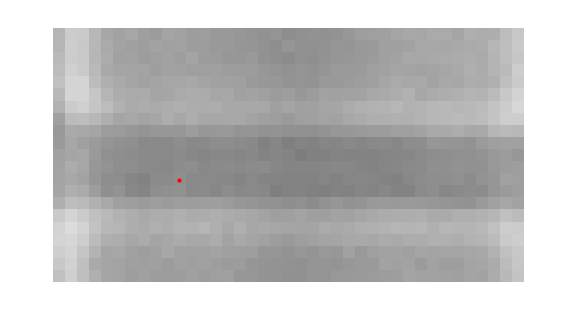
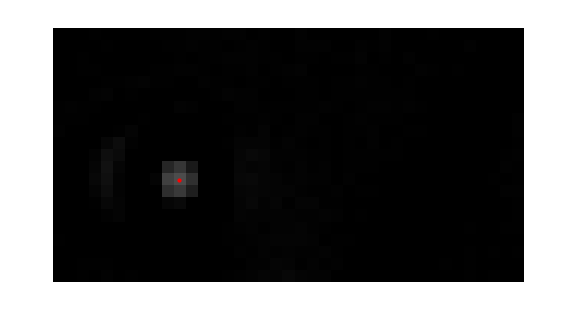
-Graphics--Graphics--Graphics--Graphics-

Area→{1→8.125}

Elongation→{1→0.209431}

FindThreshold→0.0961392

```mathematica
frame =0 60 30         +0 30           +90;
frame = 4936;
If[!IntegerQ[frame]|| 0>=frame||frame >  VideoLength[], frame = 1; Print@"Frame out of range. set to 1."];
ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list[[;;,{2,3}]]},ImageSize->Large]

curPos = VideoAnalyseFrame[frame]
Row[{
ShowTrackOverlayed[ VideoGet[frame] , curPos],
ShowTrackOverlayed[ BackgroundCurrent[], curPos],
ShowTrackOverlayed[ VideoGetForeground@VideoGet[frame] , curPos] ,
ShowTrackOverlayed[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] , curPos]
}]

"Area"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Area"]

"Elongation"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Elongation"]
"FindThreshold"-> FindThreshold@VideoGetForeground@VideoGet[frame]
```

```mathematica
8.489+ N@ROICurrent[]⟦1⟧⟦2⟧
```

197.489

```mathematica
ROICurrent[]
```

{{71,189},{110,210}}

```mathematica
LaplacianGaussianFilter[img, {30, 10}]//ColorNegate//ImageAdjust
```

## Step 5 - Select file range and run analysis

```mathematica
analyseTheseFiles = FileNames["low_conc_square_wave_(starts_+1V_on_right)2_*.avi","E:\\Experiments\\Antony\\2015-02-12\\",1][[1]]
```

```mathematica
analyseTheseFiles=Select[
(StringReplace[VideoFile[], RegularExpression["\\d+.avi"]-> ""]~~ToString@#~~".avi")&/@ (Range[1,200])
,
FileExistsQ];
```

#### Run the analysis

===================== 200fps_s1.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 9998]]

Analysis took (load + recognition): 39.3767 + 38.3943 = 77.771 sec

Particles found: 1729, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s1.csv

===================== 200fps_s2.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 46.3263 + 38.3894 = 84.7157 sec

Particles found: 1763, and problems were in 5 frames

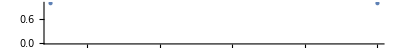

Background
-Graphics- | 4283
-Graphics- | 4283
-Graphics- | 4283
-Graphics- | 4283
-Graphics-
4283
-Graphics- | 4283
-Graphics- | 4289
-Graphics- | 4289
-Graphics- | 4290
-Graphics-
4290
-Graphics- | 4291
-Graphics- | 4291
-Graphics- | 4292
-Graphics- | 4292
-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s2.csv

===================== 200fps_s3.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 53.6118 + 39.7652 = 93.377 sec

Particles found: 1937, and problems were in 2 frames

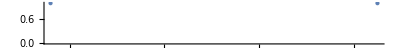

Background
-Graphics- | 4199
-Graphics- | 4199
-Graphics- | 4199
-Graphics- | 4199
-Graphics-
4199
-Graphics- | 4199
-Graphics- | 4199
-Graphics- | 4199
-Graphics- | 9377
-Graphics-
9377
-Graphics- | 9377
-Graphics- | 9377
-Graphics- | 9377
-Graphics- | 9377
-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s3.csv

===================== 200fps_s4.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 50.7075 + 40.8975 = 91.6051 sec

Particles found: 2204, and problems were in 1 frames

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s4.csv

===================== 200fps_s5.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 42.005 + 37.3237 = 79.3287 sec

Particles found: 1417, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s5.csv

===================== 200fps_s6.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 45.1114 + 39.2121 = 84.3235 sec

Particles found: 1854, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s6.csv

===================== 200fps_s7.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 57.613 + 37.9971 = 95.6101 sec

Particles found: 1656, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s7.csv

===================== 200fps_s8.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.6114 + 38.465 = 76.0764 sec

Particles found: 2061, and problems were in 2 frames

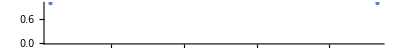

Background
-Graphics- | 5117
-Graphics- | 5117
-Graphics- | 5117
-Graphics- | 5117
-Graphics-
5117
-Graphics- | 5117
-Graphics- | 5117
-Graphics- | 5117
-Graphics- | 5566
-Graphics-
5566
-Graphics- | 5566
-Graphics- | 5566
-Graphics- | 5566
-Graphics- | 5566
-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s8.csv

===================== 200fps_s9.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.9762 + 34.0205 = 70.9967 sec

Particles found: 1063, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s9.csv

===================== 200fps_s10.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.0003 + 38.3525 = 75.3528 sec

Particles found: 1811, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s10.csv

===================== 200fps_s11.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 136.152 + 38.7011 = 174.853 sec

Particles found: 1991, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s11.csv

===================== 200fps_s12.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.3125 + 36.3117 = 73.6242 sec

Particles found: 1609, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s12.csv

===================== 200fps_s13.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.3802 + 36.525 = 73.9052 sec

Particles found: 1537, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s13.csv

===================== 200fps_s14.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.0611 + 35.1016 = 72.1626 sec

Particles found: 1317, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s14.csv

===================== 200fps_s15.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.4195 + 35.325 = 72.7445 sec

Particles found: 1347, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s15.csv

===================== 200fps_s16.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.8463 + 34.3566 = 71.2029 sec

Particles found: 1168, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s16.csv

===================== 200fps_s17.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.4742 + 33.4446 = 70.9188 sec

Particles found: 981, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s17.csv

===================== 200fps_s18.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.0657 + 36.1496 = 73.2153 sec

Particles found: 1493, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s18.csv

===================== 200fps_s19.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.5252 + 34.9943 = 72.5195 sec

Particles found: 1293, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s19.csv

===================== 200fps_s20.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.488 + 35.0545 = 72.5426 sec

Particles found: 1365, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s20.csv

===================== 200fps_s21.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.9544 + 37.0124 = 73.9669 sec

Particles found: 1765, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s21.csv

===================== 200fps_s22.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.4663 + 39.4607 = 76.9269 sec

Particles found: 2181, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s22.csv

===================== 200fps_s23.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.9851 + 36.2304 = 73.2155 sec

Particles found: 1632, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s23.csv

===================== 200fps_s24.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 8007]]

Analysis took (load + recognition): 30.093 + 29.5388 = 59.6318 sec

Particles found: 1341, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s24.csv

===================== 200fps_s25.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 9998]]

Analysis took (load + recognition): 37.1087 + 40.1208 = 77.2295 sec

Particles found: 2464, and problems were in 6 frames

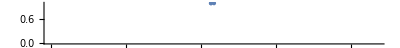

Background
-Graphics- | 5347
-Graphics- | 5347
-Graphics- | 5347
-Graphics- | 5348
-Graphics-
5348
-Graphics- | 5349
-Graphics- | 5447
-Graphics- | 5447
-Graphics- | 5447
-Graphics-
5448
-Graphics- | 5448
-Graphics- | 5449
-Graphics- | 5449
-Graphics- | 5449
-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s25.csv

===================== 200fps_s26.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.0917 + 38.6989 = 75.7906 sec

Particles found: 2058, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s26.csv

===================== 200fps_s27.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.0754 + 39.6707 = 76.7461 sec

Particles found: 2312, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s27.csv

===================== 200fps_s28.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.1651 + 40.3263 = 77.4914 sec

Particles found: 2412, and problems were in 22 frames

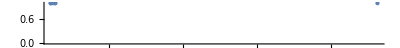

Background
-Graphics- | 2105
-Graphics- | 2106
-Graphics- | 2106
-Graphics- | 2108
-Graphics-
2110
-Graphics- | 2110
-Graphics- | 2110
-Graphics- | 2113
-Graphics- | 2118
-Graphics-
2119
-Graphics- | 2122
-Graphics- | 2123
-Graphics- | 2137
-Graphics- | 4313
-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s28.csv

===================== 200fps_s29.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 179.946 + 39.2118 = 219.158 sec

Particles found: 1996, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s29.csv

===================== 200fps_s30.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 38.0004 + 37.9667 = 75.9671 sec

Particles found: 1741, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s30.csv

===================== 200fps_s31.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.9204 + 39.1269 = 76.0473 sec

Particles found: 2143, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s31.csv

===================== 200fps_s32.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.9991 + 39.2544 = 76.2535 sec

Particles found: 2343, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s32.csv

===================== 200fps_s33.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.1177 + 39.4062 = 76.524 sec

Particles found: 2254, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s33.csv

===================== 200fps_s34.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.2567 + 36.4425 = 73.6992 sec

Particles found: 1553, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s34.csv

===================== 200fps_s35.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.9722 + 43.5897 = 80.5619 sec

Particles found: 3211, and problems were in 20 frames

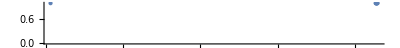

Background
-Graphics- | 88
-Graphics- | 6410
-Graphics- | 6415
-Graphics- | 6416
-Graphics-
6418
-Graphics- | 6418
-Graphics- | 6425
-Graphics- | 6425
-Graphics- | 6433
-Graphics-
6433
-Graphics- | 6434
-Graphics- | 6434
-Graphics- | 6438
-Graphics- | 6439
-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s35.csv

===================== 200fps_s36.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.9866 + 35.8836 = 72.8702 sec

Particles found: 1423, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s36.csv

===================== 200fps_s37.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.8782 + 38.2303 = 75.1085 sec

Particles found: 2031, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s37.csv

===================== 200fps_s38.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 37.2861 + 36.3863 = 73.6724 sec

Particles found: 1638, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s38.csv

===================== 200fps_s39.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 36.9802 + 41.753 = 78.7332 sec

Particles found: 2829, and problems were in 8 frames

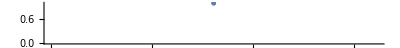

Background
-Graphics- | 2418
-Graphics- | 2419
-Graphics- | 2419
-Graphics- | 2420
-Graphics-
2420
-Graphics- | 2421
-Graphics- | 2423
-Graphics- | 2423
-Graphics- | 2423
-Graphics-
2424
-Graphics- | 2425
-Graphics- | 2425
-Graphics- | 2427
-Graphics- | 2427
-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s39.csv

===================== 200fps_s40.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 2204]]

Analysis took (load + recognition): 8.38053 + 7.99963 = 16.3802 sec

Particles found: 344, and problems were in 1 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s40.csv

===================== 200fps_s41.avi =====================

Import::noelem: The Import element ""FrameCount"" is not present when importing as "Text".

Import::noelem: The Import element ""ImageSize"" is not present when importing as "Text".

Range::range: Range specification in Range[$Failed] does not have appropriate bounds.

VideoAddProcessRawFrame: new function count is 1

FFmpeg`Private`FFGetFrameRate::noStream: -- Message text not found -- ("video") ("G:\\2015-12-12\\3\\200fps_s41.avi")

BinaryReadList::innf: Non-negative integer or Infinity expected at position 3 in ….

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧].

Image::imgarray: The specified argument Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧] should be an array of rank 2 or 3 with machine-sized numbers.

ImageDimensions::imginv: Expecting an image or graphics instead of Image[Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧], "Byte"].

PixelValue::imginv: Expecting an image or graphics instead of Image[Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧], "Byte"].

PixelValue::imginv: Expecting an image or graphics instead of "Byte".

ImageTrim::imginv: Expecting an image or graphics instead of Image[Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧], "Byte"].

ColorConvert::ccvinput: ImageTrim[Image[Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧], "Byte"], {{62.5, 499.5}, {161.5, 518.5}}] should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Import::noelem: The Import element ""FrameCount"" is not present when importing as "Text".

General::stop: Further output of Import :: noelem will be suppressed during this calculation.

Set::shape: Lists {VideoIO`Private`stream$51866399, VideoIO`Private`dim$51866399} and FFInputStreamAt["G:\\2015-12-12\\3\\200fps_s41.avi", 1, $Failed] are not the same shape.

Part::span: 1 ;; Do[(If[ImageQ[#1], Sow[#1], Throw[VideoIO`Private`i - 1]] &)[VideoIO`Private`VideoProcessRawFrame[VideoIO`Private`i, FFGetNextFrame[VideoIO`Private`stream$51866399, VideoIO`Private`dim$51866399]]], {VideoIO`Private`i, VideoIO`Private`expectedNoOfFrames$51866399}] is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Range::range: Range specification in Range[Image[Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧], "Byte"] + 256\ (256\ "Byte" + 1 ;; 4)] does not have appropriate bounds.

Range::range: Range specification in Range[Image[Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧], "Byte"] + 256\ (256\ "Byte" + ImageDimensions[Image[Partition[« 2 »], "Byte"]] ⟦ 2 ⟧)] does not have appropriate bounds.

General::stop: Further output of Range :: range will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 4 in {Range[Image[Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧], "Byte"] + 256\ (256\ "Byte" + 1 ;; 4)], Range[Image[Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧], "Byte"] + 256\ (256\ "Byte" + ImageDimensions[Image[« 2 »]] ⟦ 2 ⟧)]}.

Part::span: 1 ;; Do[(If[ImageQ[#1], Sow[#1], Throw[VideoIO`Private`i - 1]] &)[VideoIO`Private`VideoProcessRawFrame[VideoIO`Private`i, FFGetNextFrame[VideoIO`Private`stream$51866399, VideoIO`Private`dim$51866399]]], {VideoIO`Private`i, VideoIO`Private`expectedNoOfFrames$51866399}] is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stream: VideoIO`Private`stream$51866399 is not a string, InputStream[ ], or OutputStream[ ].

Background Estimate: initial algorithm failed, using backup BackgroundFnMedian algorithm

Analysing: frames [[1 ;; 4]]

Analysis took (load + recognition): 0.359297 + 0.000445095 = 0.359742 sec

Particles found: 4, and problems were in 0 frames

-Graphics-

Done: G:\2015-12-12\3\raw_points\200fps_s41.csv

G:\2015-12-12\3\raw_points\video_tracking_paramters.txt

FFmpeg`Private`FFGetFrameRate::noStream: -- Message text not found -- ("video") ("G:\\2015-12-12\\3\\200fps_s41.avi")

Part::partw: Part 1 of {} does not exist.

FFmpeg`Private`FFGetFrameRate::noStream: -- Message text not found -- ("video") ("G:\\2015-12-12\\3\\200fps_s41.avi")

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

BinaryReadList::innf: Non-negative integer or Infinity expected at position 3 in ….

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧].

Image::imgarray: The specified argument Partition[Partition[$Failed, 1], {} ⟦ 1 ⟧] should be an array of rank 2 or 3 with machine-sized numbers.

```mathematica
Monitor[
Do[ processVideo[analyseTheseFiles⟦i⟧], {i, Length[analyseTheseFiles] }],
Row[{"Analysing files: ",ProgressIndicator[i,{1,Length[analyseTheseFiles]}],i}," "]
]

Export[
 FileNameJoin[{ DirectoryName@First[analyseTheseFiles], "raw_points", "video_tracking_paramters.txt"}]     ,
ToString@{
"ROI" -> ToString@ROICurrent[],
"VideoTracking" ->Options[VideoTracking]
}
]

Export[
 FileNameJoin[{ DirectoryName@First[analyseTheseFiles], "raw_points", "sample_frame.png"}]     ,
FFImport[VideoFile[], {"Frames", 1}]
];
```